# Fig. 3: Amplitude-Squared Squeezing

## 1. Packages and Compatibility

```mathematica
Needs[ "Wolfram`QuantumFramework`"];
```

```mathematica
Needs[ "Wolfram`QuantumFramework`SecondQuantization`"];
```

```mathematica
Clear[ sqFigures];
```

```mathematica
Clear[ X, dX2, ψi, displaced, Φ, nOp];
```

```mathematica
SubValues[ Wolfram`QuantumFramework`QuantumOperator] = SubValues[Wolfram`QuantumFramework`QuantumOperator] /. HoldPattern[Wolfram`Arrays`ArrayContract[{tensor1_, tensor2_}, pairs_]] :> Wolfram`Arrays`ArrayContract[Inactive[TensorProduct][tensor1, tensor2], pairs];
```

```mathematica
With[ {propertySymbol = ToExpression[First[Names["Wolfram`QuantumFramework`*`QuantumCircuitOperatorProp"]]]}, DownValues[propertySymbol] = DownValues[propertySymbol] /. HoldPattern[ResourceFunction["LookupPart"]] :> Function[{array, index, default}, If[-Length[array] <= index <= Length[array], array[[index]], default]]];
```

```mathematica
SetFockSpaceSize[ 80];
```

## 2. Quantum States and Observables

```mathematica
nOp = With[{a = AnnihilationOperator[]}, a["Dagger"][a]];
```

```mathematica
X[ θ_] := X[θ] = With[{a = AnnihilationOperator[]}, QuantumOperator[(1/2)*(Exp[I*θ]*a^2 + Exp[(-I)*θ]*a["Dagger"]^2)]];
```

```mathematica
ψi[ m_, r_, φ_, ϕ_] := ψi[m, r, φ, ϕ] = Nest[SuperDagger[AnnihilationOperator[]][#1] & , CatState[][Association[α -> N[r*Exp[I*φ]], ϕ -> N[ϕ]]], m]["Normalize"];
```

```mathematica
displaced[ m_, r_, φ_, ϕ_, s_] := displaced[m, r, φ, ϕ, s] = With[{ψ = ψi[m, r, φ, ϕ]}, (DisplacementOperator[#1][ψ] & ) /@ {N[s]/2, -N[s]/2}];
```

```mathematica
Φ[ m_, r_, φ_, ϕ_, s_, δ1_, δ2_] := With[{w = Exp[I*N[δ1]]*Tan[N[δ2]/2], ab = displaced[m, r, φ, ϕ, s]}, ((1 + w)*ab[[1]] + (1 - w)*ab[[2]])["Normalize"]];
```

```mathematica
dX2[ m_, r_, φ_, ϕ_, s_, δ1_, δ2_, θ_] := With[{psi = Φ[m, r, φ, ϕ, s, δ1, δ2]}, Re[OperatorVariance[psi, X[θ]]] - Abs[Re[Tr[psi["Operator"][nOp]]] + 1/2]];
```

## 3. Fixed Parameters

```mathematica
r0 = 1;
```

```mathematica
φ0 = Pi/2;
```

```mathematica
ϕ0 = 0;
```

```mathematica
s0 = 0.5;
```

```mathematica
δ10 = Pi/2;
```

```mathematica
δ20 = 8 Pi/9;
```

```mathematica
m0 = 1;
```

```mathematica
θ0 = 0;
```

## 4. Scan Values

```mathematica
ms = Range[0, 4];
```

```mathematica
ss = {0, 0.3, 0.5, 0.7, 1.};
```

```mathematica
θs = {0, Pi/4, Pi/2, 3*(Pi/4), Pi};
```

```mathematica
d2s = {1, 3, 5, 7, 8}*(Pi/9);
```

```mathematica
rs = {0.5, 1, 2, 3, 4};
```

## 5. Line Styles, Markers, and Legends

```mathematica
ClearAll[ ecsFigure, ecsMarker, ecsLegend, ecsPiLabel, ecsChooseLegend];
```

```mathematica
ecsWidth = (86/25.4)*72;
```

```mathematica
ecsFont = "Times New Roman";
```

```mathematica
ecsColors = {RGBColor[1, 0.24, 0.24], RGBColor[0.16, 0.24, 1], RGBColor[0, 0.68, 0.18], RGBColor[1, 0.5, 0], RGBColor[0.7, 0, 0.74]};
```

```mathematica
ecsStyles = MapThread[Directive[#1, AbsoluteThickness[1.35], AbsoluteDashing[#2]] & , {ecsColors, {{4, 2}, {1, 1.8}, {4, 2}, {4, 1.8, 1, 1.8}, {5, 2}}}];
```

```mathematica
ecsPiLabel[ n_Integer, d_Integer] := If[n == 0, "0", StringJoin[If[n == 1, "", ToString[n]], "π/", ToString[d]]];
```

```mathematica
ecsMarker[ i_] := Graphics[{EdgeForm[Directive[ecsColors[[i]], AbsoluteThickness[0.9]]], FaceForm[White], Switch[i, 1, Disk[{0, 0}, 1], 2, Polygon[{{0, 1}, {-0.866, -0.5}, {0.866, -0.5}}], 3, Polygon[{{0, 1}, {1, 0}, {0, -1}, {-1, 0}}], 4, Rectangle[{-1, -1}, {1, 1}], 5, Polygon[{{0, -1}, {-0.866, 0.5}, {0.866, 0.5}}]]}, PlotRange -> {{-1.2, 1.2}, {-1.2, 1.2}}, ImagePadding -> 0, ImageSize -> 4, AspectRatio -> 1];
```

```mathematica
ecsLegend[ labels_] := Grid[Table[{Graphics[{ecsStyles[[i]], Line[{{0, 0.5}, {1, 0.5}}], Inset[ecsMarker[i], {0.5, 0.5}, Center, Offset[{4., 4.}]]}, PlotRange -> {{0, 1}, {0, 1}}, ImagePadding -> 0, ImageSize -> {19, 7}], labels[[i]]}, {i, 5}], Alignment -> {Left, Center}, Spacings -> {0.4, 0.06}, BaseStyle -> {FontFamily -> ecsFont, FontSize -> 10.5, Black}];
```

## 6. Automatic Legend Placement

```mathematica
ecsChooseLegend[ lines_, xr_, yr_, legendDims_, threshold_] := Module[{dense, locs, w, h, pad = 0.014, cands, b, pt, span, dr, extra, minimum, counts}, dense = Flatten[Table[Flatten[Table[Table[(1 - t)*lines[[i,j]] + t*lines[[i,j + 1]], {t, 0, 1, 0.1}], {j, Length[lines[[i]]] - 1}], 1], {i, Length[lines]}], 1]; locs = {{0.98, 0.98, 1, 1}, {0.02, 0.98, 0, 1}, {0.98, 0.02, 1, 0}, {0.02, 0.02, 0, 0}, {0.5, 0.1, 0.5, 0}, {0.5, 0.98, 0.5, 1}}; w = (legendDims[[1]] + 3)/(ecsWidth - 47); h = (legendDims[[2]] + 3)/((ecsWidth - 47)*0.64); cands = {}; Do[span = Subtract @@ Reverse[yr]; dr = yr + {0, extra*span}; pt = ({Rescale[#1[[1]], xr], Rescale[#1[[2]], dr]} & ) /@ dense; If[NumericQ[threshold], pt = Join[pt, Table[{t, Rescale[threshold, dr]}, {t, 0, 1, 0.01}]]]; Do[b = {loc[[1]] - loc[[3]]*w, loc[[1]] + (1 - loc[[3]])*w, loc[[2]] - loc[[4]]*h, loc[[2]] + (1 - loc[[4]])*h}; counts = Count[pt, {u_, v_} /; b[[1]] - pad <= u <= b[[2]] + pad && b[[3]] - pad <= v <= b[[4]] + pad]; AppendTo[cands, {counts, extra, First[First[Position[locs, loc]]], dr, loc, b}]; , {loc, locs}]; , {extra, {0, 0.04, 0.08, 0.12, 0.18, 0.25, 0.35, 0.5, 0.7}}]; minimum = First[SortBy[cands, {#1[[1]] & , #1[[2]] & , #1[[3]] & }]]; minimum];
```

## 7. Base Panel Format

```mathematica
ecsFigure[ data_, panel_Integer] := Module[{isM, isTheta, xlabel, ylabel, labels, legend, legendDims, lines, xr, yr, span, threshold, placement, loc, xticks, yticks, xminor, yminor, ymajor, step, digits, allx, ally, markerIndices, markers, graph}, isM = MemberQ[{3, 6}, panel]; isTheta = MemberQ[{4, 7}, panel]; xlabel = Which[isM, "m", isTheta, "θ", True, Subscript["δ", "2"]]; ylabel = Row[{Style["Y", Italic], "(", Style["θ", Italic], ")"}]; labels = Which[panel == 5, Table[Row[{Style["θ", Italic], " = ", ecsPiLabel[n, 4]}], {n, 0, 4}], panel == 6, Table[Row[{Subscript[Style["δ", Italic], "2"], " = ", ecsPiLabel[n, 9]}], {n, {1, 3, 5, 7, 8}}], panel == 7, (Row[{Style["r", Italic], " = ", #1}] & ) /@ {"0.5", "1", "2", "3", "4"}, True, (Row[{Style["s", Italic], " = ", #1}] & ) /@ {"0.0", "0.3", "0.5", "0.7", "1.0"}]; legend = ecsLegend[labels]; legendDims = UsingFrontEnd[ImageDimensions[Rasterize[legend, "Image", ImageResolution -> 72]]]; lines = N[data]; allx = Flatten[lines[[All,All,1]]]; ally = Flatten[lines[[All,All,2]]]; xr = MinMax[allx]; xr += 0.022*(xr[[2]] - xr[[1]])*{-1, 1}; xr[[1]] = Min[0, xr[[1]]]; threshold = 0; yr = MinMax[If[NumericQ[threshold], Append[ally, threshold], ally]]; span = yr[[2]] - yr[[1]]; yr += span*{-0.04, 0.06}; placement = ecsChooseLegend[lines, xr, yr, legendDims, threshold]; yr = placement[[4]]; loc = placement[[5]]; xticks = Which[isM, Table[{i, ToString[i], {0.017, 0}}, {i, 0, 4}], isTheta, Table[{N[n*(Pi/4)], ecsPiLabel[n, 4], {0.017, 0}}, {n, 0, 4}], True, Table[{N[n*(Pi/9)], ecsPiLabel[n, 9], {0.017, 0}}, {n, 0, 8, 2}]]; xminor = Which[isM, Range[0, 4, 0.2], isTheta, N[Range[0, 20]*(Pi/20)], True, N[Range[0, 17]*(Pi/18)]]; xminor = Select[xminor, Min[Abs[#1 - xticks[[All,1]]]] > 10^(-7) & ]; xticks = Join[xticks, ({#1, "", {0.009, 0}} & ) /@ xminor]; (ymajor = Select[N[FindDivisions[yr, 6]], yr[[1]] <= #1 <= yr[[2]] & ]; step = If[Length[ymajor] > 1, Min[Differences[ymajor]], span/5]; digits = SelectFirst[Range[0, 6], Abs[step*10^#1 - Round[step*10^#1]] < 10^(-7) & , 6]; yticks = ({#1, If[digits == 0, ToString[Round[#1]], ToString[NumberForm[If[Abs[#1] < 10^(-10), 0., #1], {Infinity, digits}, NumberPadding -> {"", "0"}], StandardForm]], {0.017, 0}} & ) /@ ymajor; yminor = Select[Flatten[Table[ymajor[[i]] + Range[1, 3]*(step/4), {i, Max[0, Length[ymajor] - 1]}]], yr[[1]] <= #1 <= yr[[2]] & ]; ); yminor = Select[yminor, Min[Abs[#1 - yticks[[All,1]]]] > 10^(-7) & ]; yticks = Join[yticks, ({#1, "", {0.009, 0}} & ) /@ yminor]; markers = Flatten[Table[markerIndices = DeleteDuplicates[Append[Range[1, Length[lines[[i]]], If[isM, 1, 3]], Length[lines[[i]]]]]; Table[Inset[ecsMarker[i], lines[[i,j]], Center, Offset[{4., 4.}]], {j, markerIndices}], {i, 5}], 1]; graph = ListLinePlot[lines, PlotStyle -> ecsStyles, Axes -> False, Frame -> True, FrameLabel -> {xlabel, ylabel}, FrameTicks -> {{yticks, ({#1[[1]], "", #1[[3]]} & ) /@ yticks}, {xticks, ({#1[[1]], "", #1[[3]]} & ) /@ xticks}}, FrameStyle -> Directive[Black, AbsoluteThickness[1.25]], FrameTicksStyle -> Directive[Black, AbsoluteThickness[0.9], FontSize -> 24, FontFamily -> ecsFont, FontWeight -> Bold], GridLines -> If[NumericQ[threshold], {None, {{threshold, Directive[GrayLevel[0.6], AbsoluteThickness[0.65], AbsoluteDashing[{3, 2}]]}}}, None], PlotRange -> {xr, yr}, PlotRangePadding -> None, LabelStyle -> {FontFamily -> ecsFont, FontSize -> 36, Black, ScriptSizeMultipliers -> 0.85}, BaseStyle -> {FontFamily -> ecsFont, FontSize -> 11}, ImagePadding -> {{39, 8}, {30, 8}}, ImageSize -> {ecsWidth, 170}, AspectRatio -> 0.64, Background -> White, Epilog -> Join[markers, {Inset[legend, Scaled[loc[[1 ;; 2]]], {Which[loc[[3]] == 1, Right, loc[[3]] == 0, Left, True, Center], If[loc[[4]] == 1, Top, Bottom]}]}]]; graph];
```

## 8. Y-Axis Ticks

```mathematica
ClearAll[ sqLatestFigure, sqComposite];
```

```mathematica
sqOrder = {5, 2, 3, 6, 4, 7};
```

```mathematica
ClearAll[ sqYTickLabel, sqCompleteYAxis];
```

```mathematica
sqYTickLabel[ value_, digits_Integer] := Module[{q = Round[Abs[value]*10^digits], sign}, sign = If[value < -10^(-10), "−", ""]; StringJoin[sign, If[digits == 0, ToString[q], StringJoin[ToString[Quotient[q, 10^digits]], ".", IntegerString[Mod[q, 10^digits], 10, digits]]]]];
```

```mathematica
sqCompleteYAxis[ g_Graphics] := Module[{pr, ft, step, lo, hi, major, minor, digits, ticks}, pr = PlotRange /. Options[g, PlotRange]; ft = FrameTicks /. Options[g, FrameTicks]; step = 1; lo = Ceiling[pr[[2,1]] - 10^(-9)]; hi = Floor[pr[[2,2]] + 10^(-9)]; digits = SelectFirst[Range[0, 6], IntegerQ[step*10^#1] & , 6]; major = Table[{N[v], sqYTickLabel[v, digits], {0.017, 0}}, {v, lo, hi, step}]; minor = {}; ticks = Join[major, minor]; ft[[1]] = {ticks, ({#1[[1]], "", #1[[3]]} & ) /@ ticks}; Show[g, PlotRange -> pr, FrameTicks -> ft]];
```

## 9. Panel Labels and Legend Positions

```mathematica
sqLatestFigure[ data_, j_Integer] := Module[{g, ep, n, letter}, g = ecsFigure[data, j]; ep = Epilog /. Options[g, Epilog]; If[j == 6, ep[[-1]] = ReplacePart[ep[[-1]], {2 -> Scaled[{0.5, 0.96}], 3 -> {Center, Top}}]]; If[j == 3, ep[[-1,1]] = ReplacePart[ep[[-1,1]], 1 -> Partition[Flatten[First[ep[[-1,1]]], 1], 4, 4, {1, 1}, ""]]; ep[[-1]] = ReplacePart[ep[[-1]], {2 -> Scaled[{0.52, 0.96}], 3 -> {Center, Top}}]]; If[MemberQ[{4, 5}, j], ep[[-1]] = ReplacePart[ep[[-1]], {2 -> Scaled[{0.98, 0.98}], 3 -> {Right, Top}}]]; n = First[First[Position[sqOrder, j]]]; letter = FromCharacterCode[96 + n]; ep = Append[ep, Inset[Style[StringJoin["(", letter, ")"], FontFamily -> "Times New Roman", FontSize -> 21, FontWeight -> "Bold", Black], Offset[{27, -1}, Scaled[{0, 1}]], {Left, Top}]]; sqCompleteYAxis[Show[g, ImagePadding -> {{39, 8}, {42, 8}}, ImageSize -> {(86/25.4)*72, 182}, PlotRangeClipping -> False, Epilog -> ep]]];
```

## 10. Panel Data

### (a) Vary delta2 for Different theta

```mathematica
sqFigures[ {"y", 5}] = sqLatestFigure[Table[Table[{δ2, dX2[m0, r0, φ0, ϕ0, s0, δ10, δ2, θ]}, {δ2, Pi/40, (8.5*Pi)/9, Pi/40}], {θ, θs}], 5];
```

### (b) Vary delta2 for Different s

```mathematica
sqFigures[ {"y", 2}] = sqLatestFigure[Table[Table[{δ2, dX2[m0, r0, φ0, ϕ0, s, δ10, δ2, θ0]}, {δ2, Pi/40, (8.5*Pi)/9, Pi/40}], {s, ss}], 2];
```

### (c) Vary m for Different s

```mathematica
sqFigures[ {"y", 3}] = sqLatestFigure[Table[Table[{m, dX2[m, r0, φ0, ϕ0, s, δ10, δ20, θ0]}, {m, ms}], {s, ss}], 3];
```

### (d) Vary m for Different delta2

```mathematica
sqFigures[ {"y", 6}] = sqLatestFigure[Table[Table[{m, dX2[m, r0, φ0, ϕ0, s0, δ10, δ2, θ0]}, {m, ms}], {δ2, d2s}], 6];
```

### (e) Vary theta for Different s

```mathematica
sqFigures[ {"y", 4}] = sqLatestFigure[Table[Table[{θ, dX2[m0, r0, φ0, ϕ0, s, δ10, δ20, θ]}, {θ, 0, Pi, Pi/60}], {s, ss}], 4];
```

### (f) Vary theta for Different r

```mathematica
sqFigures[ {"y", 7}] = sqLatestFigure[Table[Table[{θ, dX2[m0, r, φ0, ϕ0, s0, δ10, δ20, θ]}, {θ, 0, Pi, Pi/60}], {r, rs}], 7];
```

## 11. Six-Panel Layout

```mathematica
sqComposite[ ] := Module[{pw = (86/25.4)*72 - 47, ph, top = 5, bottom = 68, lefts = {472, 20, 20}, right = 12, rowGap = -12, widths, xpos, tw, th, h, panels}, ph = 1.5*(0.64*pw + 45) - 45; h = ph + top + bottom; widths = pw + right + lefts; tw = Total[widths]; th = 2*h + rowGap; xpos = Prepend[Most[Accumulate[widths]], 0]; panels = Table[Module[{g = sqFigures[{"y", sqOrder[[n]]}], col = 1 + Mod[n - 1, 3], labels}, labels = FrameLabel /. Options[g, FrameLabel]; If[col > 1, labels[[1,1]] = None]; Show[g, FrameLabel -> labels, ImagePadding -> {{lefts[[col]], right}, {bottom, top}}, ImageSize -> {widths[[col]], h}, AspectRatio -> ph/pw]], {n, 6}]; Graphics[Table[Inset[panels[[n]], {xpos[[1 + Mod[n - 1, 3]]], th - Floor[(n - 1)/3]*(h + rowGap)}, {Left, Top}, {widths[[1 + Mod[n - 1, 3]]], h}], {n, 6}], PlotRange -> {{0, tw}, {0, th}}, ImagePadding -> 0, PlotRangePadding -> None, ImageSize -> {tw, th}, AspectRatio -> th/tw, Background -> White]];
```

## 12. Final Figure

```mathematica
ClearAll[ sqFinalFigure];
```

```mathematica
sqFinalFigure[ ] := Module[{grow, g, items, panel, ticks, ep, cross, redQ, changeMarker, range, size, gap = 8, scale = 1.5}, grow[gr_Graphics] := Module[{primitives = First[gr], opts = Rest[List @@ gr]}, Graphics[primitives /. Inset[p_Graphics, pos_, anchor_, sz_List] :> Inset[grow[p], scale*pos, anchor, scale*sz], Sequence @@ (opts /. {HoldPattern[ImageSize -> sz_List] :> ImageSize -> scale*sz, HoldPattern[ImagePadding -> pad_List] :> ImagePadding -> scale*pad, HoldPattern[PlotRange -> pr_List] /; MatchQ[primitives, {_Inset..}] :> PlotRange -> scale*pr})]]; g = grow[sqComposite[]] /. {HoldPattern[FontSize -> (v_)?NumericQ] :> FontSize -> Switch[v, 10.5, 18, 11, 18, 14, 24, 21, 32, 25, 34, _, v], AbsoluteThickness[1.35] -> AbsoluteThickness[2.7], AbsoluteThickness[1.25] -> AbsoluteThickness[1.6], AbsoluteThickness[0.9] -> AbsoluteThickness[1.2], Offset[v_List] :> Offset[scale*v], Offset[v_List, p_] :> Offset[scale*v, p]}; cross = Graphics[{RGBColor[1, 0.24, 0.24], AbsoluteThickness[1.4], Line[{{-1, 0}, {1, 0}}], Line[{{0, -1}, {0, 1}}]}, PlotRange -> {{-1.2, 1.2}, {-1.2, 1.2}}, ImagePadding -> 0, ImageSize -> 10, AspectRatio -> 1]; redQ[item_] := MatchQ[item, Inset[_Graphics, _List, Center, Offset[_List]]] &&  !FreeQ[item, RGBColor[1, 0.24, 0.24]] &&  !FreeQ[item, _Disk]; changeMarker[e_] := e /. HoldPattern[Inset[marker_Graphics, pos_, anchor_, Offset[_List]]] /;  !FreeQ[marker, RGBColor[1, 0.24, 0.24]] &&  !FreeQ[marker, _Disk] :> Inset[cross, pos, anchor, Offset[{10, 10}]]; items = First[g]; Do[panel = items[[i,1]] /. Grid[rows_, opts___] :> Grid[rows, Sequence @@ DeleteCases[{opts}, HoldPattern[Alignment -> _]], Alignment -> Left]; If[i == 6, ticks = FrameTicks /. Options[panel, FrameTicks]; ticks[[1,1]] = (If[NumericQ[#1[[1]]] && OddQ[Round[#1[[1]]]], ReplacePart[#1, 2 -> ""], #1] & ) /@ ticks[[1,1]]; panel = Show[panel, FrameTicks -> ticks]]; panel = panel /. {legend_Grid :> (legend /. HoldPattern[FontSize -> _?NumericQ] :> FontSize -> 25.92), HoldPattern[Inset[Style[tag_String, style___], Offset[{_, dy_}, _Scaled], align_]] /; StringMatchQ[tag, "("~~LetterCharacter~~")"] :> Inset[Style[tag, Sequence @@ ({style} /. HoldPattern[FontSize -> _?NumericQ] :> FontSize -> 46.08)], Offset[{Switch[tag, "(b)", 40.5, "(c)", 0, _, 10], dy}, Scaled[{0, 1}]], align]}; If[i == 1, ep = Epilog /. Options[panel, Epilog]; ep = changeMarker[Join[Select[ep,  !redQ[#1] & ], Select[ep, redQ]]]; panel = Show[panel, Epilog -> ep]]; If[i >= 3, panel = panel /. legend_Grid :> (legend /. {HoldPattern[Spacings -> _] :> Spacings -> {0.4, -0.06}, HoldPattern[ImageSize -> {28.5, 10.5}] /; i == 3 :> ImageSize -> {16, 10.5}})]; items[[i,1]] = panel; If[MemberQ[{3, 6}, i], items[[i,2]] += {gap, 0}], {i, Length[items]}]; range = PlotRange /. Options[g, PlotRange]; size = ImageSize /. Options[g, ImageSize]; range[[1,2]] += gap; size[[1]] += gap; Magnify[Graphics[items, Sequence @@ DeleteCases[Options[g], HoldPattern[PlotRange | ImageSize | AspectRatio -> _]], PlotRange -> range, ImageSize -> size, AspectRatio -> size[[2]]/size[[1]]], 1.5]];
```

```mathematica
x = sqFinalFigure[];
```

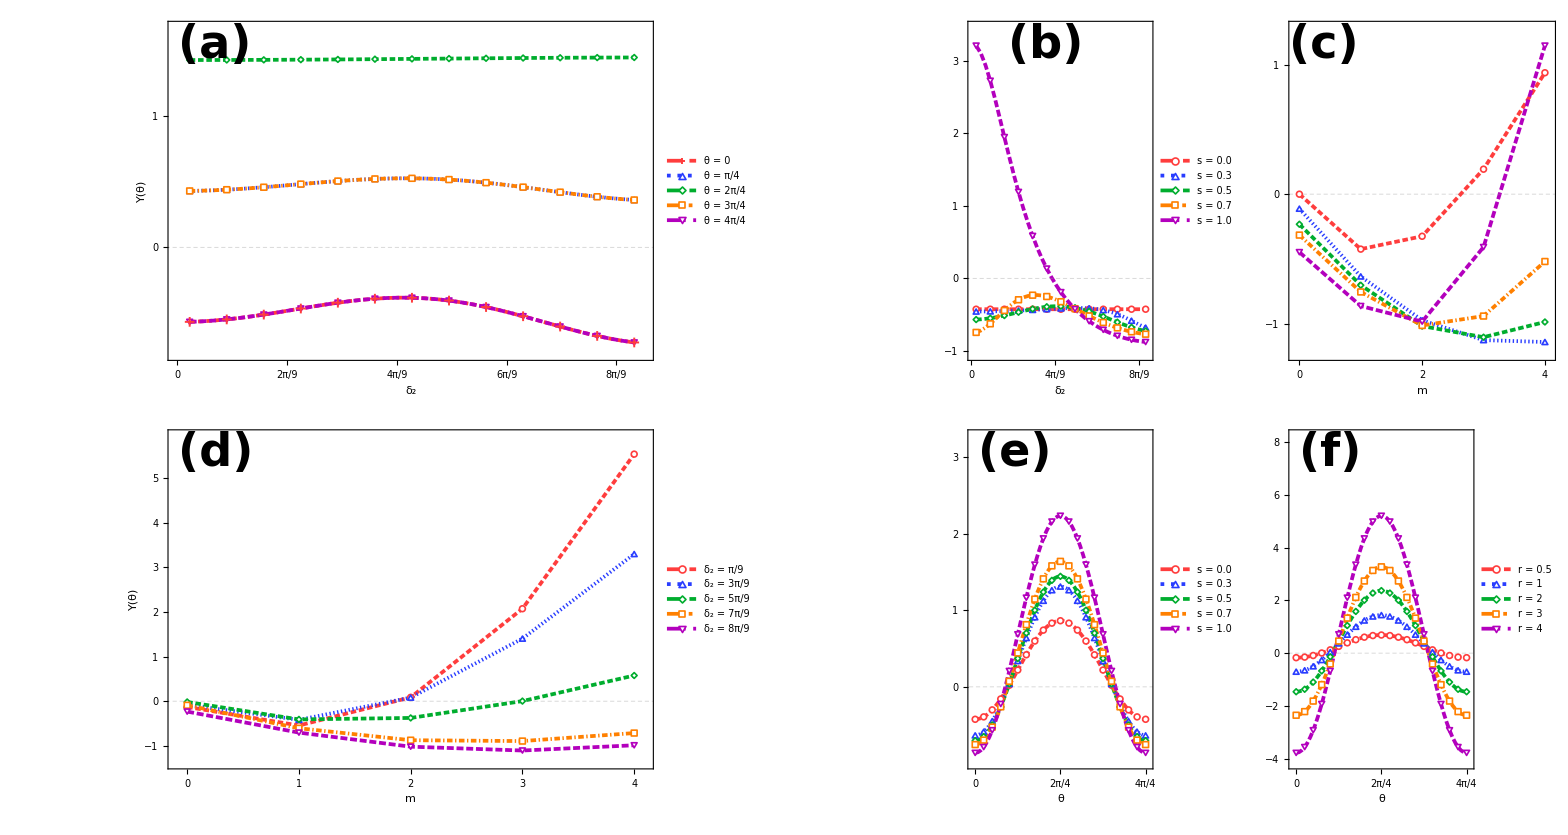

```mathematica
x
```

## 13. Export PNG (Optional)

```mathematica
Export[ FileNameJoin[{NotebookDirectory[], "Fig.3_Concise.png"}], ImageCrop[Rasterize[x, "Image", RasterSize -> 4200, Background -> White]], "PNG"];
```